This notebook is to study the effect of gamma for kinetic+rotation energy on length distribution.

```mathematica
A=2
J=4

Jkrgamma=Table[u/.FindRoot[A×x^-3×ⅇ^(-J×x)×(ⅇ^-u+gamma×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-u×l))-1,{u,-0.0001}],{gamma,{1,10,100,1000,10000}},{x,0.1,20,0.1}]
```

2

4

{{7.20688,4.79291,3.43537,2.67658,2.22125,1.90675,1.66741,1.47463,1.31397,1.17712,1.05884,0.955521,0.864566,0.784004,0.7123,0.648223,0.590768,0.539102,0.492525,0.450445,0.412352,0.37781,0.346438,0.317906,0.291923,0.268234,0.246613,0.22686,0.208798,0.192267,0.177126,0.163248,0.150518,0.138835,0.128106,0.118247,0.109183,0.100845,0.0931724,0.0861081,0.0796012,0.0736054,0.0680783,0.0629815,0.0582797,0.0539409,0.0499358,0.0462376,0.0428218,0.0396658,0.0367493,0.0340532,0.0315603,0.0292547,0.0271219,0.0251485,0.0233222,0.0216316,0.0200664,0.018617,0.0172745,0.0160309,0.0148786,0.0138109,0.0128213,0.0119039,0.0110534,0.0102647,0.00953337,0.008855,0.00822572,0.00764189,0.00710016,0.00659744,0.00613086,0.00569777,0.00529572,0.00492244,0.00457585,0.00425399,0.00395507,0.00367744,0.00341954,0.00317996,0.00295736,0.00275054,0.00255835,0.00237974,0.00221375,0.00205945,0.001916,0.00178261,0.00165852,0.001543,0.00143533,0.00133482,0.00124078,0.00115256,0.0010695,0.000991015,0.000916547,0.000845592,0.0007777,0.000712473,0.000649565,0.000588673,0.000529538,0.000471936,0.000415675,0.00036059,0.000306539,0.000253401,0.000201072,0.000149462,0.0000984932,0.0000480979,-1.78189×10^-6,-0.000051197,-0.000100192,-0.000148805,-0.00019707,-0.000245019,-0.000292676,-0.000340066,-0.000387209,-0.000434124,-0.000480828,-0.000527336,-0.000573661,-0.000619815,-0.000665809,-0.000711653,-0.000757356,-0.000802927,-0.000848372,-0.000893699,-0.000938914,-0.000984023,-0.00102903,-0.00107394,-0.00111876,-0.00116349,-0.00120814,-0.00125271,-0.00129721,-0.00134163,-0.00138598,-0.00143026,-0.00147448,-0.00151863,-0.00156273,-0.00160677,-0.00165075,-0.00169467,-0.00173855,-0.00178237,-0.00182615,-0.00186988,-0.00191356,-0.0019572,-0.00200079,-0.00204434,-0.00208786,-0.00213133,-0.00217476,-0.00221816,-0.00226152,-0.00230484,-0.00234813,-0.00239139,-0.00243461,-0.0024778,-0.00252096,-0.00256408,-0.00260718,-0.00265025,-0.00269329,-0.0027363,-0.00277929,-0.00282225,-0.00286518,-0.00290808,-0.00295096,-0.00299382,-0.00303665,-0.00307946,-0.00312224,-0.00316501,-0.00320775,-0.00325046,-0.00329316,-0.00333584,-0.00337849,-0.00342112,-0.00346374,-0.00350633,-0.00354891,-0.00359146,-0.003634,-0.00367652},{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.0021082,0.00196193,0.00182588,0.00169929,0.00158142,0.00147158,0.00136907,0.00127321,0.00118334,0.00109881,0.00101903,0.000943427,0.000871484,0.000802738,0.000736776,0.000673238,0.000611809,0.000552217,0.000494227,0.000437637,0.000382274,0.00032799,0.000274657,0.000222165,0.00017042,0.00011934,0.0000688554,0.000018904,-0.0000305672,-0.0000796045,-0.000128249,-0.000176535,-0.000224495,-0.000272157,-0.000319544,-0.000366679,-0.000413581,-0.000460267,-0.000506753,-0.000553053,-0.000599179,-0.000645142,-0.000690954,-0.000736622,-0.000782156,-0.000827564,-0.000872852,-0.000918026,-0.000963093,-0.00100806,-0.00105293,-0.0010977,-0.00114239,-0.001187,-0.00123152,-0.00127597,-0.00132035,-0.00136465,-0.00140889,-0.00145306,-0.00149717,-0.00154122,-0.00158522,-0.00162915,-0.00167303,-0.00171687,-0.00176065,-0.00180438,-0.00184806,-0.0018917,-0.00193529,-0.00197884,-0.00202235,-0.00206582,-0.00210925,-0.00215264,-0.002196,-0.00223931,-0.0022826,-0.00232584,-0.00236906,-0.00241224,-0.00245539,-0.00249851,-0.0025416,-0.00258466,-0.00262769,-0.00267069,-0.00271366,-0.00275661,-0.00279953,-0.00284242,-0.00288529,-0.00292814,-0.00297095,-0.00301375,-0.00305652,-0.00309927,-0.003142,-0.0031847,-0.00322739,-0.00327005,-0.00331269,-0.00335531,-0.00339791,-0.00344049},{7.5533,5.90431,5.01887,4.38677,3.88622,3.47035,3.11585,2.80888,2.54023,2.30323,2.09282,1.90507,1.73683,1.58553,1.44907,1.32569,1.21391,1.11245,1.02022,0.93627,0.859757,0.78995,0.726199,0.667928,0.614622,0.565822,0.521116,0.480134,0.442542,0.408042,0.37636,0.347253,0.320498,0.295894,0.273257,0.252423,0.23324,0.21557,0.199288,0.184279,0.170441,0.157676,0.145899,0.13503,0.124995,0.115728,0.107169,0.0992606,0.091952,0.085196,0.0789495,0.0731727,0.0678291,0.0628853,0.0583103,0.0540758,0.0501558,0.0465262,0.0431649,0.0400515,0.0371672,0.0344948,0.0320183,0.029723,0.0275953,0.0256227,0.0237935,0.0220973,0.0205239,0.0190645,0.0177105,0.0164543,0.0152885,0.0142065,0.0132023,0.0122701,0.0114046,0.0106011,0.00985489,0.00916194,0.00851835,0.00792056,0.00736524,0.00684933,0.00637,0.0059246,0.00551072,0.00512607,0.00476857,0.00443628,0.00412739,0.00384023,0.00357326,0.00332504,0.00309423,0.0028796,0.00268,0.00249436,0.0023217,0.0021611,0.00201169,0.00187269,0.00174331,0.00162285,0.00151059,0.00140586,0.00130797,0.00121626,0.00113009,0.00104885,0.000971969,0.000898907,0.00082919,0.000762391,0.000698132,0.000636085,0.000575964,0.000517523,0.000460549,0.000404859,0.000350298,0.00029673,0.00024404,0.000192129,0.00014091,0.0000903089,0.0000402619,-9.28727×10^-6,-0.0000583874,-0.000107081,-0.000155406,-0.000203394,-0.000251075,-0.000298474,-0.000345614,-0.000392515,-0.000439195,-0.000485671,-0.000531956,-0.000578065,-0.000624007,-0.000669795,-0.000715438,-0.000760944,-0.000806321,-0.000851578,-0.00089672,-0.000941753,-0.000986683,-0.00103152,-0.00107626,-0.00112091,-0.00116548,-0.00120996,-0.00125437,-0.00129871,-0.00134297,-0.00138717,-0.0014313,-0.00147537,-0.00151938,-0.00156334,-0.00160723,-0.00165107,-0.00169486,-0.0017386,-0.0017823,-0.00182594,-0.00186954,-0.00191309,-0.0019566,-0.00200007,-0.0020435,-0.00208689,-0.00213025,-0.00217356,-0.00221684,-0.00226009,-0.0023033,-0.00234647,-0.00238962,-0.00243273,-0.00247581,-0.00251886,-0.00256189,-0.00260488,-0.00264785,-0.00269078,-0.0027337,-0.00277658,-0.00281944,-0.00286227,-0.00290508,-0.00294787,-0.00299063,-0.00303337,-0.00307609,-0.00311878,-0.00316145,-0.0032041},{8.29867,6.91981,6.08741,5.45688,4.93576,4.48606,4.08882,3.73334,3.41296,3.12306,2.86014,2.62132,2.4041,2.2063,2.02596,1.86136,1.71098,1.57345,1.44758,1.33229,1.22662,1.12972,1.0408,0.959186,0.884229,0.815363,0.752068,0.693874,0.640349,0.591103,0.54578,0.504053,0.465625,0.430226,0.397607,0.36754,0.33982,0.314255,0.290672,0.268911,0.248827,0.230287,0.213166,0.197354,0.182746,0.169248,0.156773,0.14524,0.134578,0.124716,0.115595,0.107156,0.0993479,0.0921211,0.0854315,0.0792381,0.0735031,0.0681917,0.0632718,0.0587139,0.0544906,0.0505769,0.0469495,0.0435869,0.0404694,0.0375788,0.0348982,0.0324119,0.0301057,0.0279662,0.0259812,0.0241391,0.0224297,0.0208431,0.0193703,0.0180031,0.0167337,0.0155551,0.0144606,0.013444,0.0124999,0.0116229,0.0108082,0.0100513,0.00934802,0.00869452,0.00808723,0.00752284,0.00699826,0.00651066,0.00605739,0.00563601,0.00524424,0.00487998,0.00454126,0.00422629,0.00393337,0.00366094,0.00340755,0.00317186,0.00295261,0.00274865,0.0025589,0.00238236,0.0022181,0.00206525,0.00192299,0.00179058,0.00166727,0.00155237,0.00144519,0.00134506,0.00125132,0.00116333,0.00108048,0.00100216,0.000927845,0.000857038,0.000789295,0.000724222,0.000661474,0.000600751,0.000541794,0.000484379,0.000428312,0.000373429,0.000319586,0.000266663,0.000214553,0.000163166,0.000112423,0.0000622569,0.0000126081,-0.0000365746,-0.0000853361,-0.000133716,-0.000181748,-0.000229462,-0.000276887,-0.000324045,-0.000370957,-0.000417643,-0.000464119,-0.0005104,-0.0005565,-0.000602431,-0.000648204,-0.000693829,-0.000739315,-0.000784671,-0.000829903,-0.000875019,-0.000920025,-0.000964928,-0.00100973,-0.00105444,-0.00109906,-0.0011436,-0.00118805,-0.00123243,-0.00127673,-0.00132096,-0.00136512,-0.00140922,-0.00145325,-0.00149723,-0.00154114,-0.001585,-0.00162881,-0.00167256,-0.00171627,-0.00175992,-0.00180353,-0.00184709,-0.00189061,-0.00193409,-0.00197752,-0.00202092,-0.00206427,-0.00210759,-0.00215087,-0.00219411,-0.00223732,-0.0022805,-0.00232364,-0.00236675,-0.00240983,-0.00245288,-0.0024959,-0.00253888,-0.00258184,-0.00262478,-0.00266768,-0.00271056,-0.00275341,-0.00279624,-0.00283904,-0.00288182,-0.00292457,-0.0029673},{9.31059,8.02652,7.21071,6.57965,6.04961,5.5845,5.16572,4.78272,4.42916,4.1011,3.79599,3.51213,3.24821,3.00314,2.77587,2.56537,2.37059,2.19048,2.02402,1.87022,1.72815,1.59693,1.47574,1.36383,1.26048,1.16505,1.07693,0.995569,0.92044,0.851069,0.787011,0.727859,0.673232,0.622782,0.576186,0.533145,0.493384,0.456649,0.422705,0.391338,0.362347,0.335549,0.310775,0.287869,0.266687,0.247096,0.228974,0.212209,0.196696,0.182341,0.169054,0.156755,0.145368,0.134824,0.12506,0.116017,0.107639,0.0998778,0.0926862,0.0860218,0.0798449,0.0741192,0.0688112,0.0638896,0.0593258,0.0550933,0.0511676,0.047526,0.0441476,0.0410129,0.0381042,0.0354047,0.0328992,0.0305736,0.0284146,0.0264101,0.0245489,0.0228207,0.0212156,0.0197249,0.0183402,0.0170539,0.0158589,0.0147487,0.013717,0.0127584,0.0118674,0.0110394,0.0102698,0.0095544,0.00888936,0.00827108,0.00769624,0.00716174,0.00666472,0.00620253,0.00577268,0.00537291,0.00500107,0.00465519,0.00433344,0.00403412,0.00375566,0.00349657,0.0032555,0.00303119,0.00282246,0.00262821,0.00244743,0.00227918,0.00212258,0.00197681,0.00184108,0.00171469,0.00159691,0.00148707,0.0013845,0.00128854,0.00119855,0.0011139,0.001034,0.000958299,0.000886278,0.00081748,0.000751495,0.00068796,0.000626559,0.00056702,0.000509104,0.000452608,0.000397356,0.000343199,0.000290005,0.000237664,0.00018608,0.000135169,0.0000848597,0.0000350895,-0.0000141956,-0.000063043,-0.000111494,-0.000159585,-0.000207348,-0.000254811,-0.000301999,-0.000348934,-0.000395637,-0.000442123,-0.00048841,-0.000534511,-0.000580439,-0.000626205,-0.000671821,-0.000717295,-0.000762635,-0.000807851,-0.000852948,-0.000897933,-0.000942813,-0.000987593,-0.00103228,-0.00107687,-0.00112138,-0.00116581,-0.00121015,-0.00125443,-0.00129863,-0.00134276,-0.00138683,-0.00143083,-0.00147477,-0.00151866,-0.00156249,-0.00160626,-0.00164998,-0.00169365,-0.00173728,-0.00178085,-0.00182438,-0.00186787,-0.00191131,-0.00195471,-0.00199808,-0.0020414,-0.00208468,-0.00212793,-0.00217114,-0.00221432,-0.00225746,-0.00230058,-0.00234365,-0.0023867,-0.00242972,-0.0024727,-0.00251566,-0.00255859,-0.00260149,-0.00264437,-0.00268722,-0.00273004}}

```mathematica
Gamma1 = Jkrgamma[[1]]
Gamma2 = Jkrgamma[[2]]
Gamma3= Jkrgamma[[3]]
Gamma4=Jkrgamma[[4]]
Gamma5= Jkrgamma[[5]]
```

{7.20688,4.79291,3.43537,2.67658,2.22125,1.90675,1.66741,1.47463,1.31397,1.17712,1.05884,0.955521,0.864566,0.784004,0.7123,0.648223,0.590768,0.539102,0.492525,0.450445,0.412352,0.37781,0.346438,0.317906,0.291923,0.268234,0.246613,0.22686,0.208798,0.192267,0.177126,0.163248,0.150518,0.138835,0.128106,0.118247,0.109183,0.100845,0.0931724,0.0861081,0.0796012,0.0736054,0.0680783,0.0629815,0.0582797,0.0539409,0.0499358,0.0462376,0.0428218,0.0396658,0.0367493,0.0340532,0.0315603,0.0292547,0.0271219,0.0251485,0.0233222,0.0216316,0.0200664,0.018617,0.0172745,0.0160309,0.0148786,0.0138109,0.0128213,0.0119039,0.0110534,0.0102647,0.00953337,0.008855,0.00822572,0.00764189,0.00710016,0.00659744,0.00613086,0.00569777,0.00529572,0.00492244,0.00457585,0.00425399,0.00395507,0.00367744,0.00341954,0.00317996,0.00295736,0.00275054,0.00255835,0.00237974,0.00221375,0.00205945,0.001916,0.00178261,0.00165852,0.001543,0.00143533,0.00133482,0.00124078,0.00115256,0.0010695,0.000991015,0.000916547,0.000845592,0.0007777,0.000712473,0.000649565,0.000588673,0.000529538,0.000471936,0.000415675,0.00036059,0.000306539,0.000253401,0.000201072,0.000149462,0.0000984932,0.0000480979,-1.78189×10^-6,-0.000051197,-0.000100192,-0.000148805,-0.00019707,-0.000245019,-0.000292676,-0.000340066,-0.000387209,-0.000434124,-0.000480828,-0.000527336,-0.000573661,-0.000619815,-0.000665809,-0.000711653,-0.000757356,-0.000802927,-0.000848372,-0.000893699,-0.000938914,-0.000984023,-0.00102903,-0.00107394,-0.00111876,-0.00116349,-0.00120814,-0.00125271,-0.00129721,-0.00134163,-0.00138598,-0.00143026,-0.00147448,-0.00151863,-0.00156273,-0.00160677,-0.00165075,-0.00169467,-0.00173855,-0.00178237,-0.00182615,-0.00186988,-0.00191356,-0.0019572,-0.00200079,-0.00204434,-0.00208786,-0.00213133,-0.00217476,-0.00221816,-0.00226152,-0.00230484,-0.00234813,-0.00239139,-0.00243461,-0.0024778,-0.00252096,-0.00256408,-0.00260718,-0.00265025,-0.00269329,-0.0027363,-0.00277929,-0.00282225,-0.00286518,-0.00290808,-0.00295096,-0.00299382,-0.00303665,-0.00307946,-0.00312224,-0.00316501,-0.00320775,-0.00325046,-0.00329316,-0.00333584,-0.00337849,-0.00342112,-0.00346374,-0.00350633,-0.00354891,-0.00359146,-0.003634,-0.00367652}

{7.25633,5.13375,4.08847,3.43477,2.96465,2.59969,2.30318,2.05513,1.84343,1.66017,1.49987,1.35854,1.23316,1.12138,1.02134,0.931495,0.850588,0.777552,0.711485,0.651611,0.597262,0.547856,0.502884,0.461899,0.424508,0.390361,0.359149,0.330594,0.304449,0.280495,0.258532,0.238381,0.219883,0.202891,0.187276,0.172917,0.159709,0.147552,0.136358,0.126048,0.116547,0.107789,0.0997122,0.0922618,0.0853868,0.0790408,0.0731812,0.0677694,0.0627696,0.0581493,0.0538786,0.04993,0.0462785,0.0429008,0.0397758,0.036884,0.0342073,0.0317294,0.029435,0.0273101,0.0253418,0.0235183,0.0218287,0.0202629,0.0188115,0.017466,0.0162186,0.0150618,0.0139889,0.0129938,0.0120706,0.0112141,0.0104193,0.00968172,0.00899715,0.00836169,0.00777177,0.00722405,0.00671547,0.00624317,0.00580454,0.00539712,0.00501866,0.00466707,0.00434042,0.00403689,0.00375485,0.00349273,0.00324912,0.00302268,0.0028122,0.00261653,0.00243462,0.00226548,0.0021082,0.00196193,0.00182588,0.00169929,0.00158142,0.00147158,0.00136907,0.00127321,0.00118334,0.00109881,0.00101903,0.000943427,0.000871484,0.000802738,0.000736776,0.000673238,0.000611809,0.000552217,0.000494227,0.000437637,0.000382274,0.00032799,0.000274657,0.000222165,0.00017042,0.00011934,0.0000688554,0.000018904,-0.0000305672,-0.0000796045,-0.000128249,-0.000176535,-0.000224495,-0.000272157,-0.000319544,-0.000366679,-0.000413581,-0.000460267,-0.000506753,-0.000553053,-0.000599179,-0.000645142,-0.000690954,-0.000736622,-0.000782156,-0.000827564,-0.000872852,-0.000918026,-0.000963093,-0.00100806,-0.00105293,-0.0010977,-0.00114239,-0.001187,-0.00123152,-0.00127597,-0.00132035,-0.00136465,-0.00140889,-0.00145306,-0.00149717,-0.00154122,-0.00158522,-0.00162915,-0.00167303,-0.00171687,-0.00176065,-0.00180438,-0.00184806,-0.0018917,-0.00193529,-0.00197884,-0.00202235,-0.00206582,-0.00210925,-0.00215264,-0.002196,-0.00223931,-0.0022826,-0.00232584,-0.00236906,-0.00241224,-0.00245539,-0.00249851,-0.0025416,-0.00258466,-0.00262769,-0.00267069,-0.00271366,-0.00275661,-0.00279953,-0.00284242,-0.00288529,-0.00292814,-0.00297095,-0.00301375,-0.00305652,-0.00309927,-0.003142,-0.0031847,-0.00322739,-0.00327005,-0.00331269,-0.00335531,-0.00339791,-0.00344049}

{7.5533,5.90431,5.01887,4.38677,3.88622,3.47035,3.11585,2.80888,2.54023,2.30323,2.09282,1.90507,1.73683,1.58553,1.44907,1.32569,1.21391,1.11245,1.02022,0.93627,0.859757,0.78995,0.726199,0.667928,0.614622,0.565822,0.521116,0.480134,0.442542,0.408042,0.37636,0.347253,0.320498,0.295894,0.273257,0.252423,0.23324,0.21557,0.199288,0.184279,0.170441,0.157676,0.145899,0.13503,0.124995,0.115728,0.107169,0.0992606,0.091952,0.085196,0.0789495,0.0731727,0.0678291,0.0628853,0.0583103,0.0540758,0.0501558,0.0465262,0.0431649,0.0400515,0.0371672,0.0344948,0.0320183,0.029723,0.0275953,0.0256227,0.0237935,0.0220973,0.0205239,0.0190645,0.0177105,0.0164543,0.0152885,0.0142065,0.0132023,0.0122701,0.0114046,0.0106011,0.00985489,0.00916194,0.00851835,0.00792056,0.00736524,0.00684933,0.00637,0.0059246,0.00551072,0.00512607,0.00476857,0.00443628,0.00412739,0.00384023,0.00357326,0.00332504,0.00309423,0.0028796,0.00268,0.00249436,0.0023217,0.0021611,0.00201169,0.00187269,0.00174331,0.00162285,0.00151059,0.00140586,0.00130797,0.00121626,0.00113009,0.00104885,0.000971969,0.000898907,0.00082919,0.000762391,0.000698132,0.000636085,0.000575964,0.000517523,0.000460549,0.000404859,0.000350298,0.00029673,0.00024404,0.000192129,0.00014091,0.0000903089,0.0000402619,-9.28727×10^-6,-0.0000583874,-0.000107081,-0.000155406,-0.000203394,-0.000251075,-0.000298474,-0.000345614,-0.000392515,-0.000439195,-0.000485671,-0.000531956,-0.000578065,-0.000624007,-0.000669795,-0.000715438,-0.000760944,-0.000806321,-0.000851578,-0.00089672,-0.000941753,-0.000986683,-0.00103152,-0.00107626,-0.00112091,-0.00116548,-0.00120996,-0.00125437,-0.00129871,-0.00134297,-0.00138717,-0.0014313,-0.00147537,-0.00151938,-0.00156334,-0.00160723,-0.00165107,-0.00169486,-0.0017386,-0.0017823,-0.00182594,-0.00186954,-0.00191309,-0.0019566,-0.00200007,-0.0020435,-0.00208689,-0.00213025,-0.00217356,-0.00221684,-0.00226009,-0.0023033,-0.00234647,-0.00238962,-0.00243273,-0.00247581,-0.00251886,-0.00256189,-0.00260488,-0.00264785,-0.00269078,-0.0027337,-0.00277658,-0.00281944,-0.00286227,-0.00290508,-0.00294787,-0.00299063,-0.00303337,-0.00307609,-0.00311878,-0.00316145,-0.0032041}

{8.29867,6.91981,6.08741,5.45688,4.93576,4.48606,4.08882,3.73334,3.41296,3.12306,2.86014,2.62132,2.4041,2.2063,2.02596,1.86136,1.71098,1.57345,1.44758,1.33229,1.22662,1.12972,1.0408,0.959186,0.884229,0.815363,0.752068,0.693874,0.640349,0.591103,0.54578,0.504053,0.465625,0.430226,0.397607,0.36754,0.33982,0.314255,0.290672,0.268911,0.248827,0.230287,0.213166,0.197354,0.182746,0.169248,0.156773,0.14524,0.134578,0.124716,0.115595,0.107156,0.0993479,0.0921211,0.0854315,0.0792381,0.0735031,0.0681917,0.0632718,0.0587139,0.0544906,0.0505769,0.0469495,0.0435869,0.0404694,0.0375788,0.0348982,0.0324119,0.0301057,0.0279662,0.0259812,0.0241391,0.0224297,0.0208431,0.0193703,0.0180031,0.0167337,0.0155551,0.0144606,0.013444,0.0124999,0.0116229,0.0108082,0.0100513,0.00934802,0.00869452,0.00808723,0.00752284,0.00699826,0.00651066,0.00605739,0.00563601,0.00524424,0.00487998,0.00454126,0.00422629,0.00393337,0.00366094,0.00340755,0.00317186,0.00295261,0.00274865,0.0025589,0.00238236,0.0022181,0.00206525,0.00192299,0.00179058,0.00166727,0.00155237,0.00144519,0.00134506,0.00125132,0.00116333,0.00108048,0.00100216,0.000927845,0.000857038,0.000789295,0.000724222,0.000661474,0.000600751,0.000541794,0.000484379,0.000428312,0.000373429,0.000319586,0.000266663,0.000214553,0.000163166,0.000112423,0.0000622569,0.0000126081,-0.0000365746,-0.0000853361,-0.000133716,-0.000181748,-0.000229462,-0.000276887,-0.000324045,-0.000370957,-0.000417643,-0.000464119,-0.0005104,-0.0005565,-0.000602431,-0.000648204,-0.000693829,-0.000739315,-0.000784671,-0.000829903,-0.000875019,-0.000920025,-0.000964928,-0.00100973,-0.00105444,-0.00109906,-0.0011436,-0.00118805,-0.00123243,-0.00127673,-0.00132096,-0.00136512,-0.00140922,-0.00145325,-0.00149723,-0.00154114,-0.001585,-0.00162881,-0.00167256,-0.00171627,-0.00175992,-0.00180353,-0.00184709,-0.00189061,-0.00193409,-0.00197752,-0.00202092,-0.00206427,-0.00210759,-0.00215087,-0.00219411,-0.00223732,-0.0022805,-0.00232364,-0.00236675,-0.00240983,-0.00245288,-0.0024959,-0.00253888,-0.00258184,-0.00262478,-0.00266768,-0.00271056,-0.00275341,-0.00279624,-0.00283904,-0.00288182,-0.00292457,-0.0029673}

{9.31059,8.02652,7.21071,6.57965,6.04961,5.5845,5.16572,4.78272,4.42916,4.1011,3.79599,3.51213,3.24821,3.00314,2.77587,2.56537,2.37059,2.19048,2.02402,1.87022,1.72815,1.59693,1.47574,1.36383,1.26048,1.16505,1.07693,0.995569,0.92044,0.851069,0.787011,0.727859,0.673232,0.622782,0.576186,0.533145,0.493384,0.456649,0.422705,0.391338,0.362347,0.335549,0.310775,0.287869,0.266687,0.247096,0.228974,0.212209,0.196696,0.182341,0.169054,0.156755,0.145368,0.134824,0.12506,0.116017,0.107639,0.0998778,0.0926862,0.0860218,0.0798449,0.0741192,0.0688112,0.0638896,0.0593258,0.0550933,0.0511676,0.047526,0.0441476,0.0410129,0.0381042,0.0354047,0.0328992,0.0305736,0.0284146,0.0264101,0.0245489,0.0228207,0.0212156,0.0197249,0.0183402,0.0170539,0.0158589,0.0147487,0.013717,0.0127584,0.0118674,0.0110394,0.0102698,0.0095544,0.00888936,0.00827108,0.00769624,0.00716174,0.00666472,0.00620253,0.00577268,0.00537291,0.00500107,0.00465519,0.00433344,0.00403412,0.00375566,0.00349657,0.0032555,0.00303119,0.00282246,0.00262821,0.00244743,0.00227918,0.00212258,0.00197681,0.00184108,0.00171469,0.00159691,0.00148707,0.0013845,0.00128854,0.00119855,0.0011139,0.001034,0.000958299,0.000886278,0.00081748,0.000751495,0.00068796,0.000626559,0.00056702,0.000509104,0.000452608,0.000397356,0.000343199,0.000290005,0.000237664,0.00018608,0.000135169,0.0000848597,0.0000350895,-0.0000141956,-0.000063043,-0.000111494,-0.000159585,-0.000207348,-0.000254811,-0.000301999,-0.000348934,-0.000395637,-0.000442123,-0.00048841,-0.000534511,-0.000580439,-0.000626205,-0.000671821,-0.000717295,-0.000762635,-0.000807851,-0.000852948,-0.000897933,-0.000942813,-0.000987593,-0.00103228,-0.00107687,-0.00112138,-0.00116581,-0.00121015,-0.00125443,-0.00129863,-0.00134276,-0.00138683,-0.00143083,-0.00147477,-0.00151866,-0.00156249,-0.00160626,-0.00164998,-0.00169365,-0.00173728,-0.00178085,-0.00182438,-0.00186787,-0.00191131,-0.00195471,-0.00199808,-0.0020414,-0.00208468,-0.00212793,-0.00217114,-0.00221432,-0.00225746,-0.00230058,-0.00234365,-0.0023867,-0.00242972,-0.0024727,-0.00251566,-0.00255859,-0.00260149,-0.00264437,-0.00268722,-0.00273004}

General::munfl: Exp[-713.481] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-720.688] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.894] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

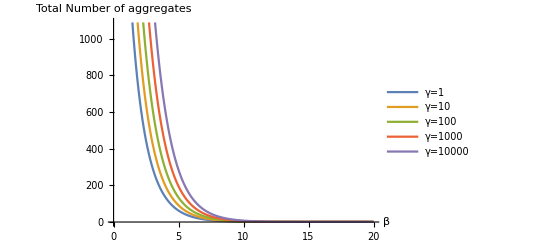

```mathematica
ListLinePlot[{(ⅇ^-Gamma1+1×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma1×l))/(ⅇ^-Gamma1+1×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma1×l))×10000,(ⅇ^-Gamma2+10×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma2×l))/(ⅇ^-Gamma2+10×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma2×l))×10000,(ⅇ^-Gamma3+100×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma3×l))/(ⅇ^-Gamma3+100×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma3×l))×10000,(ⅇ^-Gamma4+1000×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma4×l))/(ⅇ^-Gamma4+1000×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma4×l))×10000,(ⅇ^-Gamma5+10000×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma5×l))/(ⅇ^-Gamma5+10000×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma5×l))×10000},DataRange->{0,20},PlotLegends->{"γ=1","γ=10","γ=100","γ=1000","γ=10000"},AxesLabel->{"β","Total Number of aggregates"}]
```

General::munfl: Exp[-713.481] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-720.688] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-727.894] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

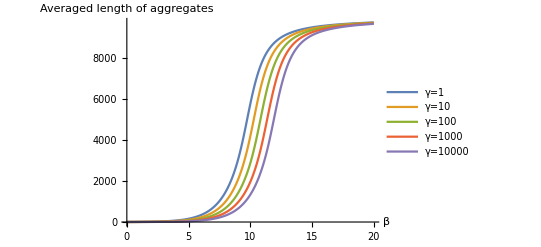

```mathematica
ListLinePlot[{(ⅇ^-Gamma1+1×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma1×l))/(ⅇ^-Gamma1+1×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma1×l)),(ⅇ^-Gamma2+10×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma2×l))/(ⅇ^-Gamma2+10×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma2×l)),(ⅇ^-Gamma3+100×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma3×l))/(ⅇ^-Gamma3+100×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma3×l)),(ⅇ^-Gamma4+1000×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma4×l))/(ⅇ^-Gamma4+1000×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma4×l)),(ⅇ^-Gamma5+10000×∑_(l=2)^10000 l^4×(l-1)^2×ⅇ^(-Gamma5×l))/(ⅇ^-Gamma5+10000×∑_(l=2)^10000 l^3×(l-1)^2×ⅇ^(-Gamma5×l))},DataRange->{0,20},PlotLegends->{"γ=1","γ=10","γ=100","γ=1000","γ=10000"},AxesLabel->{"β","Averaged length of aggregates"}]
```